## The 3-Colored GKL rule, a generalisation

#### A rule for a 1D deterministic cellular automation which leads to global consensus (or solving the “density classification problem” of deciding whether the density of initial red cells is above or below 50%) "radius 3" rule (operating on size - 7 neighborhoods) was constructed ("GKL rule") : {l3_, _, l1_, c_, r1_, _, r3_} :> If[If[c == 0, r1 + r3, l1 + l3] + c >= 2, 1, 0] {l3_, _, l1_, c_, r1_, _, r3_} /; MatchQ[r1 + r3, patt1] && MatchQ[l1 + l3, patt2]

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}/;MatchQ[r1+r3,0|1]&&MatchQ[l1+l3,0|1]:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0],2],2,3},

RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0-> Yellow ,1->Red},Frame->False]]
```

CellularAutomaton::nocol: Since position 2 of rule specification {{340282359394263022844220576404172963840,340282359315035310737233970154438656000,340279101532219677776116669985209712640,338958311018522360492699893610724761600,320266054999950853313195545240629452960,272226272881192977392706327054685077632,226856634493160728781064737424995819680},2,3} is not {}, position 1 must be an integer or a pure Boolean function.

ArrayPlot::mat: Argument CellularAutomaton[{{340282359394263022844220576404172963840,340282359315035310737233970154438656000,340279101532219677776116669985209712640,338958311018522360492699893610724761600,320266054999950853313195545240629452960,272226272881192977392706327054685077632,226856634493160728781064737424995819680},2,3},{1,0,1,1,1,1,0,1,1,1,«290»},60] at position 1 is not a list of lists.

ArrayPlot[CellularAutomaton[{{340282359394263022844220576404172963840,340282359315035310737233970154438656000,340279101532219677776116669985209712640,338958311018522360492699893610724761600,320266054999950853313195545240629452960,272226272881192977392706327054685077632,226856634493160728781064737424995819680},2,3},{1,0,1,1,1,1,0,1,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0,1,1,0,0,0,1,1,0,1,1,1,1,0,1,0,1,0,0,0,0,1,1,1,0,0,0,1,0,0,1,0,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,0,1,1,0,1,0,0,1,1,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1,0,1,1,1,1,0,0,1,1,0,1,1,1,0,1,0,1,1,1,1,0,1,0,1,0,0,0,1,0,0,1,0,1,0,1,1,1,0,1,1,1,0,1,0,0,0,1,1,1,1,1,1,1,0,0,1,1,1,0,1,1,0,0,1,1,0,1,1,1,1,0,1,1,1,1,1,0,1,0,1,1,0,0,1,0,0,1,0,1,1,1,1,0,0,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,0,0,0,1,0,1,0,0,1,0,1,0,0,1,0,0,1,1,0,0,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,1,0,1,1,1,0,1,0,1,0,1,0,1,1,1,0,1,1,0,1,1,1,0,0,0,0,0,0,1,0,1,0,1},60],ColorRules→{0→RGBColor[1, 1, 0],1→RGBColor[1, 0, 0]},Frame→False]

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {r1_,_,l3_,_,c_,_}:>If[If[c==1,r1,l3]+c>=2,1,0],2],2,3},
(*varying 2,3 of above, use different combinations*)
RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0-> Yellow ,1->Red},Frame->False]]
```

CellularAutomaton::nocol: Since position 2 of rule specification {{340282366920938463444927863358058659840,340282366841710300967557013907638845440,340277174703306882242637262502835978240,338958311018522360492699998064329424640,320265757102059730318470218759311257840,272225893536750770770699685945414569164,226854911280625642308916404954512140970},2,3} is not {}, position 1 must be an integer or a pure Boolean function.

ArrayPlot::mat: Argument CellularAutomaton[{{340282366920938463444927863358058659840,340282366841710300967557013907638845440,340277174703306882242637262502835978240,338958311018522360492699998064329424640,320265757102059730318470218759311257840,272225893536750770770699685945414569164,226854911280625642308916404954512140970},2,3},{1,0,1,1,1,1,0,1,1,1,«290»},60] at position 1 is not a list of lists.

ArrayPlot[CellularAutomaton[{{340282366920938463444927863358058659840,340282366841710300967557013907638845440,340277174703306882242637262502835978240,338958311018522360492699998064329424640,320265757102059730318470218759311257840,272225893536750770770699685945414569164,226854911280625642308916404954512140970},2,3},{1,0,1,1,1,1,0,1,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0,1,1,0,0,0,1,1,0,1,1,1,1,0,1,0,1,0,0,0,0,1,1,1,0,0,0,1,0,0,1,0,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,0,1,1,0,1,0,0,1,1,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1,0,1,1,1,1,0,0,1,1,0,1,1,1,0,1,0,1,1,1,1,0,1,0,1,0,0,0,1,0,0,1,0,1,0,1,1,1,0,1,1,1,0,1,0,0,0,1,1,1,1,1,1,1,0,0,1,1,1,0,1,1,0,0,1,1,0,1,1,1,1,0,1,1,1,1,1,0,1,0,1,1,0,0,1,0,0,1,0,1,1,1,1,0,0,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,0,0,0,1,0,1,0,0,1,0,1,0,0,1,0,0,1,1,0,0,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,1,0,1,1,1,0,1,0,1,0,1,0,1,1,1,0,1,1,0,1,1,1,0,0,0,0,0,0,1,0,1,0,1},60],ColorRules→{0→RGBColor[1, 1, 0],1→RGBColor[1, 0, 0]},Frame→False]

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {r1_,_,l3_,_,c_,_,r3_}:>If[If[c==0,r1+r3,l3]+c>=2,1,0],2],,3},
(*varying 2,3 of above, use different combinations*)
RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0-> Yellow ,1->Red},Frame->False]]
```

CellularAutomaton::kspec: Since position 1 of rule specification {333605276854913868128165575036318515200,Null,3} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

ArrayPlot::mat: Argument CellularAutomaton[{333605276854913868128165575036318515200,Null,3},{1,0,1,1,1,1,0,1,1,1,«290»},60] at position 1 is not a list of lists.

ArrayPlot[CellularAutomaton[{333605276854913868128165575036318515200,Null,3},{1,0,1,1,1,1,0,1,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0,1,1,0,0,0,1,1,0,1,1,1,1,0,1,0,1,0,0,0,0,1,1,1,0,0,0,1,0,0,1,0,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,0,1,1,0,1,0,0,1,1,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1,0,1,1,1,1,0,0,1,1,0,1,1,1,0,1,0,1,1,1,1,0,1,0,1,0,0,0,1,0,0,1,0,1,0,1,1,1,0,1,1,1,0,1,0,0,0,1,1,1,1,1,1,1,0,0,1,1,1,0,1,1,0,0,1,1,0,1,1,1,1,0,1,1,1,1,1,0,1,0,1,1,0,0,1,0,0,1,0,1,1,1,1,0,0,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,0,0,0,1,0,1,0,0,1,0,1,0,0,1,0,0,1,1,0,0,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,1,0,1,1,1,0,1,0,1,0,1,0,1,1,1,0,1,1,0,1,1,1,0,0,0,0,0,0,1,0,1,0,1},60],ColorRules→{0→RGBColor[1, 1, 0],1→RGBColor[1, 0, 0]},Frame→False]

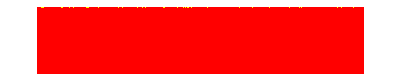

```mathematica
BlockRandom[SeedRandom[555];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors],2],2,3},

(*varying 2,3 of above, use different combinations*)
RandomChoice[{.9,.1}->{1,0},300],60],ColorRules->{0-> Yellow ,1->Red},Frame->False]]
```

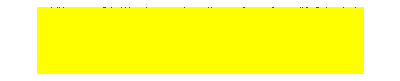

```mathematica
BlockRandom[SeedRandom[555];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors],2],2,3},

(*varying 2,3 of above, use different combinations*)
RandomChoice[{.1,.9}->{1,0},300],60],ColorRules->{0-> Yellow ,1->Red},Frame->False]]
```

```mathematica
tworule = {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0]
```

{l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c≥2,1,0]

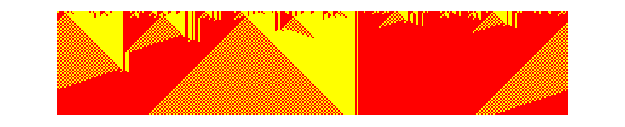

```mathematica
BlockRandom[SeedRandom[569];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,l1+l3,r1+r3]+c>=2,1,0],2],2,3},RandomChoice[{.5,.5}->{1,0},300],60],ColorRules->{0->Yellow,1-> Red},Frame->False]]
```

```mathematica
FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,l1+l3,r1+r3]+c>=2,1,0],2]
```

333636105325236971337806416870490831360

```mathematica
Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,l1+l3,r1+r3]+c>=2,1,0]
```

{1,1,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0}

```mathematica
data=ParallelTable[If[p==.5,Nothing,MeanAround/@Transpose[Table[Mean/@CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0],2],2,3},RandomChoice[{p,1-p}->{1,0},5000],200],200]]],{p,.3,.7,.05}];
ListLinePlot[MapThread[Callout[#1,Row[{Style["p",Italic],"=",#2}]]&,{data,Cases[Range[.3,.7,.05],Except[0.5]]}]]
```

-Graphics-

#### something happened at p = .5 : In a sense the cellular automaton “can’t make up its mind” and on an infinite line it generates an infinite nested sequence of domains that alternate between 0 and 1: (critical phenomena)

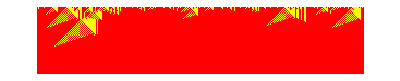

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[ (* ./ --> ReplaceAll *){FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==1,r1+r3,l1+l3]+c>=2,1,0],2],2,3},RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0-> Yellow ,1->Red},Frame->False]]
```

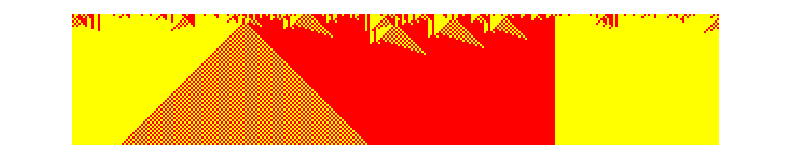

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[ {FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0],2],2,3},RandomChoice[{.4,.6}->{1,0},300],60],ColorRules->{0-> Yellow ,1->Red},Frame->False]]
```

```mathematica
FromDigits[{0,1,2,1,2,1,0,1,0},2]
```

330

```mathematica
FromDigits[{0,1,2,1,2,1,0,1,0},3]
```

4080

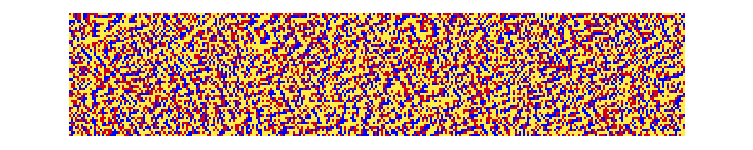

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0],2],3,3},RandomChoice[{.1,.5,.4}->{2,1,0},300],50],ColorRules->{0->Hue[0.15,0.72,1],1->Hue[0.98,1,0.8200000000000001], 2-> Blue},Frame->False]]
```

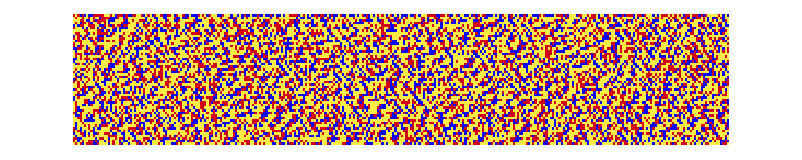

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0],2],3,3},RandomChoice[{.333,.333,.333}->{2,1,0},300],50],ColorRules->{0->Hue[0.15,0.72,1],1->Hue[0.98,1,0.8200000000000001], 2-> Blue},Frame->False]]
```

```mathematica
{l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0]
```

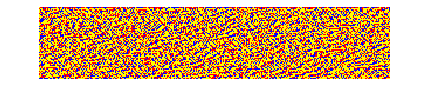
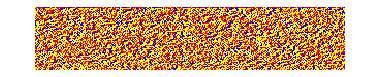
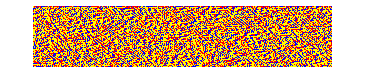

```mathematica
Table[ThreeColorCA1 = BlockRandom[SeedRandom[828];
				ArrayPlot[
				CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==i,r1+r3,l1+l3,b1+b3]+c>=3,2,1,0],2],3,3},

RandomChoice[{.4,.5, .1}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]],{i,3}]
```

rule above gives bus seat pattern

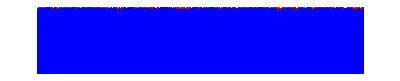
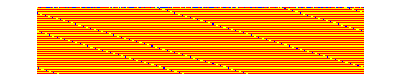
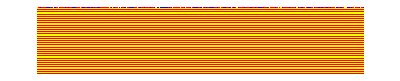
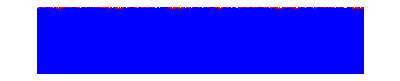
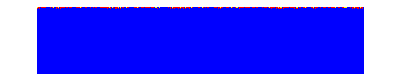
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ThreeColorCA1 = BlockRandom[SeedRandom[828];
				ArrayPlot[
				CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==i,r1+r3,b1+b3,l1+l3]+c>=3,2,1,0],3],3,k},

RandomChoice[{.4,.5, .1}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]],{i,10},{k,3,7}]
```

```mathematica
Table[ThreeColorCA1 = BlockRandom[SeedRandom[828];
				ArrayPlot[
				CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,c_,l1_,b1_,r1_,r3_}:>If[If[c==i,r1-r3,b1+b3,l1+l3]+c>=3,2,1,0],2],3,k},

RandomChoice[{.5,.4, .1}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]],{i,3},{k,3,6}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ThreeColorCA1 = BlockRandom[SeedRandom[828];
				ArrayPlot[
				CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,c_,l1_,b1_,r1_,r3_}:>If[If[c==i,r1-r3,b1-b3,l1+l3]+c>=3,2,1,0],2],3,k},

RandomChoice[{.5,.4, .1}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]],{i,3},{k,3,6}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ThreeColorCA1 = BlockRandom[SeedRandom[828];
				ArrayPlot[
				CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,c_,l1_,b1_,r1_,r3_}:>If[If[c==i,r1+r3,b1-b3,l1-l3]+c>=3,2,1,0],2],3,k},

RandomChoice[{.5,.4, .1}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]],{i,3},{k,3,6}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ThreeColorCA1 = BlockRandom[SeedRandom[828];
				ArrayPlot[
				CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,c_,l1_,b1_,r1_,r3_}:>If[If[c==i,r1+r3+b1,b1+b3,l1+l3]+c>=3,2,1,0],2],3,k},

RandomChoice[{.5,.4, .1}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]],{i,3},{k,3,6}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ThreeColorCA1 = BlockRandom[SeedRandom[828];
				ArrayPlot[
			CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==i,r1+r3,b1+b3,l1+l3]+c>=3,2,1,0],2],3,k},

RandomChoice[{.5,.4, .1}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]],{i,10},{k,3,7}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ParallelTable[ BlockRandom[SeedRandom[828];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l1_,l3_,b3_,c_,b1_,r1_,r3_}:>If[If[c==1,r1+r3,l1+l3,b1+b3]+c>=3,2,1,0],2],3,k},

RandomChoice[{.4,.5, .1}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]],{k,3,9}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BlockRandom[SeedRandom[24425];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==i,r1+r3,l1+l3]+c>=2,1,0],2],2,3},RandomChoice[{.5,.5}->{1,0},1000],500],ColorRules->{0->Yellow,1->Red},Frame->False]]
```

-Graphics-

searching for all 2^32 radius-2 rules --> achieves “approximate consensus”
below : the cells go to the “majority value” (this is the r = 2 rule 4196304428, for p = 0.6):

```mathematica
BlockRandom[SeedRandom[567]; 
 ArrayPlot[
  CellularAutomaton[{4196304428, 2, 2}, 
   RandomChoice[{.6, .4} -> {1, 0}, 500], 200], 
  ColorRules -> {0 -> Yellow, 
    1 ->  Red}, Frame -> False]]
```

-Graphics-

rule 184: doesn’t achieve consensus on “overall density”, but does do so with respect to left- and right-moving stripes, here with the nested pattern generated when p = 0.5:

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[184,RandomChoice[{1,0},400],180],ColorRules->{0->Yellow,1->Red},Frame->False]]
```

-Graphics-

Achieving consensus faster: comparison of GKL rule with another radius - 3 rule, latter has shorter average consensis time:

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.48,.52}->{1,0},800],180],ColorRules->{0-> Yellow,1->Red},Frame->False,ImageSize->{650,Automatic}]]&/@{{339789091192587366278221041213531750560,2,3},{339841014953466429132970652455676805280,2,3}}]
```

-Graphics-
-Graphics-

A more elaborate / ornate way

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[{#,3,3},RandomChoice[{.333,.333,.333}->{2,1,0},800],240],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False,ImageSize->{650,Automatic}]]&/@{337607298446901146542393000444934784552,338557163619953682141694933300561896488,313421633154342960352882914658469183496, 1018787996772,895177,771502,942851,504876,930520,290177,178737,162904,733138,844381,1018787}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

Some rules (e.g. optimal sorting rules):  optimal rules will often be ones that don’t look simple in their behavior, and that can’t realistically be constructed by standard engineering methods, 
and essentially just have to be found “experimentally” by searching the computational universe of possible rules.

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[33855716361995368214169493330056189648,SeedRandom[seed];Normal[SparseArray[Thread[RandomSample[Range[400],Round[d400]]->1],400]],250],ImageSize->{500,369},PlotRange->{{0,w},{0,w},{0,w}},PlotLabel->Text[Style["initial density "<>ToString[d],"Output",Bold]]],
{{seed,1234,"initial condition"},1000,1500,1},
{{d,0.5,"initial density"},0.002,1},Delimiter,
{{w,150,"zoom"},20,250,1}]
```

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[{294869764523995749814890097794812493824,4},SeedRandom[seed];Normal[Take[SparseArray[Thread[If[Round[d 300]==0,{},RandomSample[Range[300],Round[d 300]]]->3],400],s]],(Ceiling[2 s/3])],ImageSize->400,Frame->False],
{{seed,1234,"initial configuration"},1000,1500,1},
{{d,0.5,"initial black cell density"},0,1},Delimiter,
{{s,100,"zoom"},20,300,1}]
```